{-Graphics3D-,-Graphics-,-Graphics-,-Graphics-}

{4.77731×10^7,{BB→-0.603857,CC→1.346,DD→-674.285,EE→-1032.47,GG→375563.}}

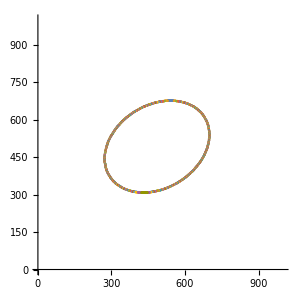
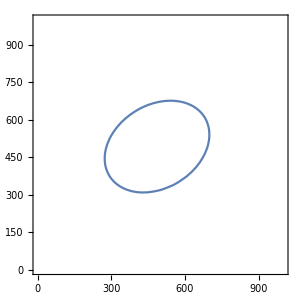

{{2,0,0},{0,2,0},{0,0,1}}

{{-1.1207,-1.34777,-0.00571726},{-1.34777,-1.22801,-0.00579573},{-0.00571726,-0.00579573,-0.0000235353}}

{{16,0,0,0},{0,36,0,0},{0,0,16,0},{0,0,0,-1}}

{{-352/3,400/3,-400/3},{400/3,-292/3,400/3},{-400/3,400/3,-352/3}}

{{-356.664,24.6632,0.000376372},{{-0.692896,-0.721031,-0.00322622},{0.721036,-0.692898,-0.000610321},{-0.00179538,-0.00274911,0.999995}}}

{{-377.552,29.5518,16.},{{1.,-0.951638,1.},{1.,2.10164,1.},{-1.,0.,1.}}}

{{-0.00584388,-0.873009,0.48767},{0.809471,-0.290466,-0.510281},{0.587131,0.391773,0.708372}}

{-46.2979,44.8973,146.286}

```mathematica
Example of Attitude Determination from Ellipsoidal Measurements;


viewpoint={1,-1,1};(* Viewpoint Vector *)
viewpoint=viewpoint/Norm[viewpoint]; (* Normalize the Viewpoint *)
focal=2; (* Focal Length *)
aa=4; (* Semiaxis a *)
bb=6; (* Semiaxis b *)
cc=4; (* Semiaxis c *)
ellipsoid=ParametricPlot3D[{aa Cos[u]Sin[v],bb Sin[u]Sin[v],cc Cos[v]},{v,0,Pi},{u,0,2Pi},Mesh->30,MeshStyle->Directive[Gray,Thickness[0.001]],PlotStyle->{GrayLevel[0.8],Opacity[1.0]},Lighting->{{"Directional", White, {{30,-60,0},{0,-5,-1}}}},Boxed->False,Axes->False,ImageSize->500,ViewPoint->viewpoint,PlotRange->focal*{{-aa,aa},{-bb,bb},{-cc,cc}}];

img=Rasterize[ellipsoid,RasterSize->1000,ImageSize->2000]; (* Rasterize to Image *)
bin=Binarize[img,0.8]; (* Binarize the Image *)
edge=EdgeDetect[bin]; (* Detect the Edge *)
edgePoints=ImageKeypoints[edge]; (* Extract the Keypoints *)
highlights=HighlightImage[img,edge]; (* Highlight the Edge *)
imgSize=300;
{
Show[ellipsoid,ImageSize->imgSize,Boxed->True],
Show[bin,ImageSize->imgSize,Boxed->True],
Show[edge,ImageSize->imgSize,Boxed->True],
Show[highlights,ImageSize->imgSize,Boxed->True]
}
(* Show the Image Processing *)

edgeData=ImageData[edge];
radii=GatherBy[PixelValuePositions[edge,1],Last];
dim=Dimensions[radii];
imgDim=Dimensions[edgeData];
MeasuredEllipse=ListPlot[radii,PlotRange->{{0,imgDim[[1]]},{0,imgDim[[2]]}},AspectRatio->1];
(* Measured Image Coordinates of the Ellipse *)

subCurve[x_,y_,BB_,CC_,DD_,EE_,GG_]:=(x^2+BB*x*y+CC*y^2+DD*x+EE*y+GG) (* Define the Ellipse Function *)
edges={};
For[i=1,i≤Length[radii],i++,
For[j=1,j≤Length[radii[[i]]],j++,edges=Append[edges,radii[[i,j]]]]];
(* Get the Measured Elliptic Coordinates *)

minima=FindMinimum[Sum[subCurve[edges[[i]][[1]],edges[[i]][[2]],BB,CC,DD,EE,GG]^2,{i,1,Length[edges]}],{BB,CC,DD,EE,GG}]
param=minima[[2]];
BBB=param[[1,2]];
CCC=param[[2,2]];
DDD=param[[3,2]];
EEE=param[[4,2]];
GGG=param[[5,2]];
(* Ellipse Fitting by Least Square *)

FittedEllipse=ContourPlot[subCurve[x,y,BBB,CCC,DDD,EEE,GGG]==0,{x,0,imgDim[[1]]},{y,0,imgDim[[2]]}];
{Show[MeasuredEllipse,ImageSize->imgSize],Show[FittedEllipse,ImageSize->imgSize]}
Kmatrix={
{focal,0,0},
{0,focal,0},
{0,0,1}
}
(* Show the Fitted Ellipse and Measurement Points *)

(* Get Required Matrices *)
AAA=1;
kk=GGG*BBB^2-BBB*DDD*EEE+CCC*DDD^2+AAA*EEE^2-4*AAA*CCC*GGG;
CimStar={
{(EEE^2-4*CCC*GGG)/(focal^2*kk),(2*BBB*GGG-DDD*EEE)/(focal^2*kk),(2*CCC*DDD-BBB*EEE)/(focal*kk)},
{(2*BBB*GGG-DDD*EEE)/(focal^2*kk),(DDD^2-4*AAA*GGG)/(focal^2*kk),(2*AAA*EEE-BBB*DDD)/(focal*kk)},
{(2*CCC*DDD-BBB*EEE)/(focal*kk),(2*AAA*EEE-BBB*DDD)/(focal*kk),(BBB^2-4*AAA*CCC)/kk}
}
Q={
{1/aa^2,0,0,0},
{0,1/bb^2,0,0},
{0,0,1/cc^2,0},
{0,0,0,-1}
};
Qstar=Inverse[Q]
Q3star=Inverse[Q[[1;;3,1;;3]]];
tw=viewpoint*focal*10;
Tw={{tw[[1]]},{tw[[2]]},{tw[[3]]}};
Bstar=Q3star-Tw.Transpose[Tw]
α=Tr[Bstar]/Tr[CimStar];
eig1=Eigensystem[α*CimStar];
eig2=Eigensystem[Bstar];
N[eig1]
N[eig2]
V=eig1[[2]];
W=eig2[[2]];
R=V.Transpose[W];

(* Orthonormalize the Rotation Matrix *)
{U,S,VV}=SingularValueDecomposition[R];
SS={
{1,0,0},
{0,1,0},
{0,0,Det[U]*Det[VV]}
};
R=U.SS.Transpose[VV]

(* The Euler Angles *)
EulerAngles[R]*180/Pi
```

```mathematica
Example of Attitude Determination from Image Correspondences;


t=ContourPlot[Cos[2x]+y,{x,0,2Pi},{y,0,2Pi},ColorFunction->"Rainbow",Frame->False,PlotRangePadding->None];
Vase=ParametricPlot3D[{u,Sin[v]*(u^3+2 u^2-2 u+2)/5,Cos[v]*(u^3+2 u^2-2 u+2)/5},{u,-2.3,1.3},{v,0,2 Pi},PlotStyle->Texture[t]]
image1=Image[Show[Vase,ViewPoint->{1.0,2.0,1.0},Boxed->False,Axes->False,Lighting->"Neutral",ImageSize->{640,480}]];
image2=Image[Show[Vase,ViewPoint->{2.0,2.0,2.0},Boxed->False,Axes->False,Lighting->"Neutral",ImageSize->{640,480}]];
matches = ImageCorrespondingPoints [image1,image2,MaxFeatures->300,Method->{"BRISK"}];
part1=Show[image1,
Graphics[{RGBColor[0.4117647058823529, 0.6900000000000001, 1],PointSize[.008],MapThread[If[True,{RGBColor[0.78, 0.91, 0],Point[#1]},{Thick,Arrowheads[Medium],Arrow[{#1,#2+{ImageDimensions[image1][[1]],0}}]}]&,matches]}]];
part2=Show[image2,
Graphics[{RGBColor[0.4117647058823529, 0.6900000000000001, 1],PointSize[.008],MapThread[If[True,{RGBColor[0.78, 0.91, 0],Point[#2]},{Thick,Arrowheads[Medium],Arrow[{#1,#2+{ImageDimensions[image2][[1]],0}}]}]&,matches]}]];
Show[ImageAssemble[{part1,part2}],
Graphics[{RGBColor[0.4117647058823529, 0.6900000000000001, 1],PointSize[.008],MapThread[If[False,{RGBColor[0.78, 0.91, 0],Point[#1]},{Thick,Arrowheads[Medium],Arrow[{#1,#2+{ImageDimensions[image1][[1]],0}}]}]&,matches]}],
ImageSize->650
]
SetDirectory[NotebookDirectory[]];
Export["match1.txt",matches[[1]],"Table","FieldSeparators"->" "];
Export["match2.txt",matches[[2]],"Table","FieldSeparators"->" "];
Export["match1.eps",image1];
Export["match2.eps",image2];
Export["match1.jpg",image1];
Export["match2.jpg",image2];
```

-Graphics3D-

-Graphics-